```mathematica
sol=DSolve[{y''[x]+λ y[x]==0,y'[0]==0,y'[1]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Cos[x √λ], n∈ℤ&&n≥0&&λ==n^2 π^2}, {0, True}}]}}

```mathematica
eigfuns=Table[y[x]/. sol[[1]]//.{n->i,λ->(Pi*n)^2}/. {C[1]->1},{i,5}]
```

{Cos[π x],Cos[2 π x],Cos[3 π x],Cos[4 π x],Cos[5 π x]}

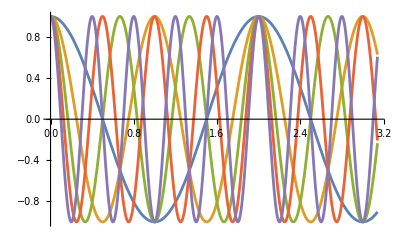

```mathematica
Plot[Evaluate[eigfuns],{x,0,Pi}]
```

```mathematica
M=Table[Integrate[eigfuns[[i]]*eigfuns[[j]],{x,0,1}],{i,1,Length[eigfuns]},{j,1,Length[eigfuns]}];
```

```mathematica
M //MatrixForm
```

(1/2 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 1/2)

```mathematica
sol2=DSolve[{y2''[x]+λ y2[x]==0,y2[0]- y2'[0]==0,y2[1]==0},y2[x],x]
```

{{y2[x]→Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}]}}

{,,,,}

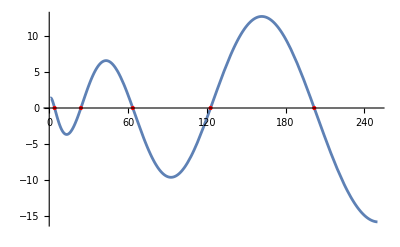

```mathematica
roots = λ /. Solve[√λ Cos[√λ]+Sin[√λ]==0 && 1< λ < 250, λ]
data = Table[{λ, 0}, {λ, roots}];
Plot[√λ Cos[√λ]+Sin[√λ], {λ, 1,250}, Epilog->{PointSize[Large], Red, Point[data]}]
```

```mathematica
eigfuns2=Table[y2[x]/. sol2[[1]],{i,5}]
```

{Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}]}

```mathematica
M2=Table[Integrate[eigfuns2[[i]]*eigfuns2[[j]],{x,0,1}],{i,1,Length[eigfuns2]},{j,1,Length[eigfuns2]}];
```